## Plotting Normaized volume vs Applied pressure

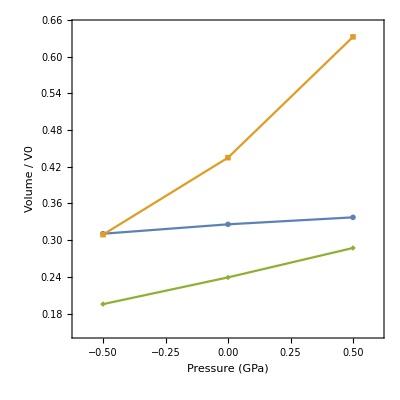

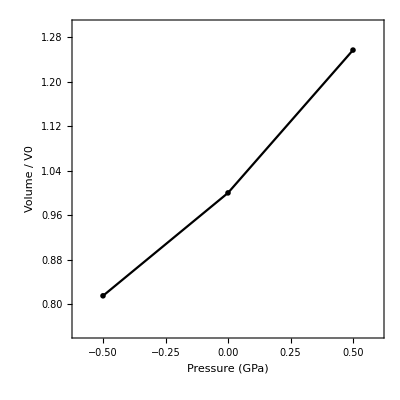

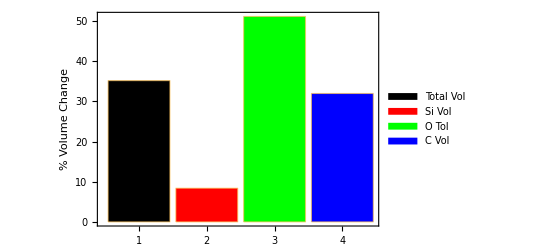

```mathematica
pC=-0.5;
peq=0;
pT=0.5;

Totshift=(1.2569-0.8149)/1.2569*100;
Sishift=(0.3373-0.3090)/0.3373*100;
Oshift=(0.6324-0.3090)/0.6324*100;
Cshift=(0.2872-0.1954)/0.2872*100;

SiVol={{pC,0.3105},{peq,0.3259},{pT,0.3373}};
OVol={{pC,0.3090},{peq,0.4349},{pT,0.6324}};
CVol={{pC,0.1954},{peq,0.2391},{pT,0.2872}};
TotVol={{pC,0.8149},{peq,1.0},{pT,1.2569}};

ListPlot[{SiVol,OVol,CVol},
PlotMarkers->{Automatic,Medium},
FrameLabel->{"Pressure (GPa)","Volume / V0"},
FrameStyle->Directive[Thick,FontSize->20,Black],
Frame->True,
AspectRatio->1,
Joined->True,
PlotRange->{{-0.6,0.6},{0.15,0.65}}]

ListPlot[{TotVol},
PlotMarkers->{Automatic,Medium},
FrameLabel->{"Pressure (GPa)","Volume / V0"},
FrameStyle->Directive[Thick,FontSize->20,Black],
Frame->True,
AspectRatio->1,
Joined->True,
PlotStyle->Black,
PlotRange->{{-0.6,0.6},{0.75,1.3}}]

BarChart[{Totshift,Sishift,Oshift,Cshift},ChartLegends->{"Total Vol","Si Vol","O Tol","C Vol"},Frame->True,FrameStyle->Directive[Medium,FontSize->20,Black],FrameLabel->{"","% Volume Change"},ChartStyle->{Black,Red,Green,Blue}]
```